## 示例：（一般不要更改）

## MPO，MPS以及缩并，

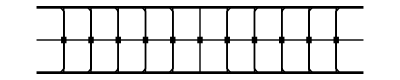

```mathematica
(*Leftcaconical  = Function[{x1,y1,h},Graphics[{Line[{{x1,y1},{x1,y1+h}}],Line[{{x1-1/8*h,y1},{x1,y1+1/8*h}}]}]];*)
ClearAll;
LeftCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1-Abs[1/8*h],y1}}]};
RightCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1+Abs[1/8*h],y1}}]};
SiteVariation[x1_,y1_,h_] := {Line[{{x1,y1},{x1,y1+h}}]};
MatrixProductOperator[x1_,y1_,s_] := Rectangle[{x1-s,y1-s},{x1+s,y1+s}];
upleg = Flatten[Table[LeftCaconicalLeg[x,0,1],{x,0,4,1}]];
botleg = Flatten[Table[LeftCaconicalLeg[x,2,-1],{x,0,4,1}]];
leftpart = Join[upleg,botleg];
upleg = Flatten[Table[RightCaconicalLeg[x,0,1],{x,6,10,1}]];
botleg = Flatten[Table[RightCaconicalLeg[x,2,-1],{x,6,10,1}]];
rightpart = Join[upleg,botleg];
mpopart = Table[MatrixProductOperator[x,1,0.1],{x,0,10,1}];
mpopart = Append[mpopart,Line[{{-1,1},{11,1}}]];
Show[Graphics[leftpart],Graphics[SiteVariation[5,2,-2]],Graphics[rightpart],Graphics[mpopart],Graphics[{Thickness[0.005],Line[{{-1,0},{11,0}}]}],Graphics[{Thickness[0.005],Line[{{-1,2},{11,2}}]}]]
```

## 单个tensor，以及少量的组合

```mathematica
ClearAll;
LeftCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1-Abs[1/8*h],y1}}]};
RightCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1+Abs[1/8*h],y1}}]};
Show[Graphics[LeftCaconicalLeg[0,0,-1]],Graphics[LeftCaconicalLeg[1,0,-1]],Graphics[{Thickness[0.005],Line[{{-1,0},{2,0}}]}]]
Show[Graphics[RightCaconicalLeg[0,0,-1]],Graphics[RightCaconicalLeg[1,0,-1]],Graphics[{Thickness[0.005],Line[{{-1,0},{2,0}}]}]]
```

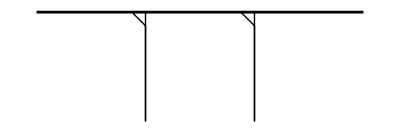

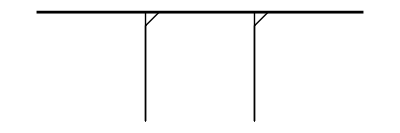

```mathematica
MatrixProductOperator[x1_,y1_,s_] := Rectangle[{x1-s,y1-s},{x1+s,y1+s}];
Show[Graphics[MatrixProductOperator[0,0,0.1]],Graphics[MatrixProductOperator[1,0,0.1]],
Graphics[Line[{{-1,0},{2,0}}]],Graphics[Line[{{0,1},{0,-1}}]],Graphics[Line[{{1,1},{1,-1}}]]]
```

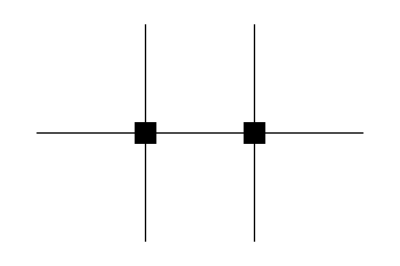

```mathematica
MatrixProductOperator[x1_,y1_,s_] := Rectangle[{x1-s,y1-s},{x1+s,y1+s}];
Show[Graphics[MatrixProductOperator[0,0,0.1]],Graphics[MatrixProductOperator[0,-1,0.1]],
Graphics[Line[{{0,1},{0,-2}}]],Graphics[Line[{{-1,0},{1,0}}]],Graphics[Line[{{-1,-1},{1,-1}}]]]
```

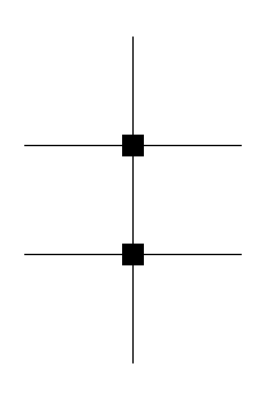

## 工作区

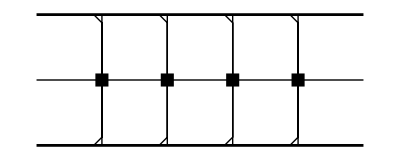

```mathematica
(*Leftcaconical  = Function[{x1,y1,h},Graphics[{Line[{{x1,y1},{x1,y1+h}}],Line[{{x1-1/8*h,y1},{x1,y1+1/8*h}}]}]];*)
ClearAll;
LeftCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1-Abs[1/8*h],y1}}]};
RightCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1+Abs[1/8*h],y1}}]};
MatrixProductOperator[x1_,y1_,s_] := Rectangle[{x1-s,y1-s},{x1+s,y1+s}];
upleg = Flatten[Table[LeftCaconicalLeg[x,0,1],{x,0,3,1}]];
botleg = Flatten[Table[LeftCaconicalLeg[x,2,-1],{x,0,3,1}]];
mpopart = Table[MatrixProductOperator[x,1,0.1],{x,0,3,1}];
mpopart = Append[mpopart,Line[{{-1,1},{4,1}}]];

Show[Graphics[upleg],Graphics[botleg],Graphics[mpopart],Graphics[{Thickness[0.005],Line[{{-1,0},{4,0}}]}],Graphics[{Thickness[0.005],Line[{{-1,2},{4,2}}]}]]
```

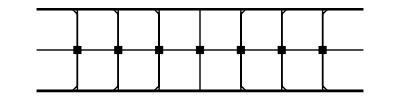

```mathematica
ClearAll;
halflength = 3;
LeftCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1-Abs[1/8*h],y1}}]};
RightCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1+Abs[1/8*h],y1}}]};
SiteVariation[x1_,y1_,h_] := {Line[{{x1,y1},{x1,y1+h}}]};
MatrixProductOperator[x1_,y1_,s_] := Rectangle[{x1-s,y1-s},{x1+s,y1+s}];
upleg = Flatten[Table[LeftCaconicalLeg[x,0,1],{x,0,halflength-1,1}]];
botleg = Flatten[Table[LeftCaconicalLeg[x,2,-1],{x,0,halflength-1,1}]];
leftpart = Join[upleg,botleg];
upleg = Flatten[Table[RightCaconicalLeg[x,0,1],{x,halflength+1,2*halflength,1}]];
botleg = Flatten[Table[RightCaconicalLeg[x,2,-1],{x,halflength+1,2*halflength,1}]];
rightpart = Join[upleg,botleg];
mpopart = Table[MatrixProductOperator[x,1,0.1],{x,0,2*halflength,1}];
mpopart = Append[mpopart,Line[{{-1,1},{2*halflength+1,1}}]];
Show[Graphics[leftpart],Graphics[SiteVariation[halflength,2,-2]],Graphics[rightpart],Graphics[mpopart],Graphics[{Thickness[0.005],Line[{{-1,0},{2*halflength+1,0}}]}],Graphics[{Thickness[0.005],Line[{{-1,2},{2*halflength+1,2}}]}]]
```

{Line[{{0,0},{0,1}}],Line[{{1,0},{1,1}}],Line[{{2,0},{2,1}}],Line[{{3,0},{3,1}}],Line[{{4,0},{4,1}}]}

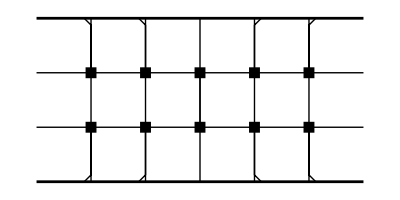

```mathematica
ClearAll;
halflength = 2;
LeftCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1-Abs[1/8*h],y1}}]};
RightCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1+Abs[1/8*h],y1}}]};
SiteVariation[x1_,y1_,h_] := {Line[{{x1,y1},{x1,y1+h}}]};
MatrixProductOperator[x1_,y1_,s_] := Rectangle[{x1-s,y1-s},{x1+s,y1+s}];
upleg = Flatten[Table[LeftCaconicalLeg[x,-1,1],{x,0,halflength-1,1}]];
botleg = Flatten[Table[LeftCaconicalLeg[x,2,-1],{x,0,halflength-1,1}]];
leftpart = Join[upleg,botleg];
upleg = Flatten[Table[RightCaconicalLeg[x,-1,1],{x,halflength+1,2*halflength,1}]];
botleg = Flatten[Table[RightCaconicalLeg[x,2,-1],{x,halflength+1,2*halflength,1}]];
rightpart = Join[upleg,botleg];
mpopart = Table[MatrixProductOperator[x,1,0.1],{x,0,2*halflength,1}];
mpopart = Append[mpopart,Line[{{-1,1},{2*halflength+1,1}}]];
mpopart2 = Table[MatrixProductOperator[x,0,0.1],{x,0,2*halflength,1}];
mpopart2= Append[mpopart2,Line[{{-1,0},{2*halflength+1,0}}]];
somelines = Table[Line[{{x,0},{x,1}}],{x,0,2*halflength,1}]
Show[Graphics[leftpart],Graphics[SiteVariation[halflength,2,-3]],Graphics[mpopart2],Graphics[rightpart],Graphics[mpopart],
Graphics[somelines],
Graphics[{Thickness[0.005],Line[{{-1,-1},{2*halflength+1,-1}}]}],Graphics[{Thickness[0.005],Line[{{-1,2},{2*halflength+1,2}}]}]]
```

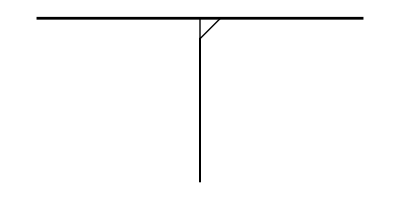

```mathematica
ClearAll;
RightCaconicalLeg[x1_,y1_,h_]  :={Line[{{x1,y1},{x1,y1+h},{x1,y1+1/8*h},{x1+Abs[1/8*h],y1}}]};

Show[Graphics[RightCaconicalLeg[0,0,-1]],Graphics[{Thickness[0.005],Line[{{-1,0},{1,0}}]}]]
```

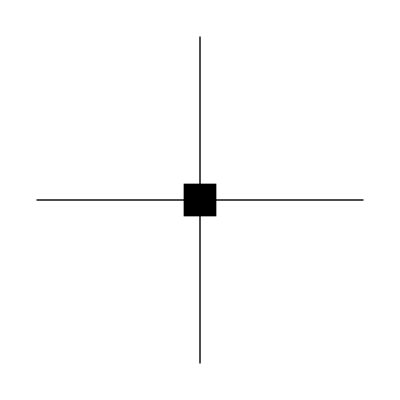

```mathematica
MatrixProductOperator[x1_,y1_,s_] := Rectangle[{x1-s,y1-s},{x1+s,y1+s}];
Show[Graphics[MatrixProductOperator[0,0,0.1]],
Graphics[Line[{{-1,0},{1,0}}]],Graphics[Line[{{0,1},{0,-1}}]]]
```